#### Igel1995

```mathematica
CmatIgel=({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
CmatIgel==Transpose[CmatIgel]
TmatIgel = Simplify[TmatOfCmat[CmatIgel]];
MatrixNote[TmatIgel]="Tmat is TmatIgel";
Print["A given Voigt matrix is ",MatrixForm[CmatIgel]];  
Print["The corresponding [T]_𝔹𝔹 is ",MatrixForm[TmatIgel]];
```

## The superlattice

```mathematica
Tmat=TmatIgel;
MatrixNote[Tmat]
```

```mathematica
WantDetails="NoWantDetails"
```

```mathematica
RangeSigmaAll={TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG};
```

```mathematica
OutputFor[Tmat,#]&/@RangeSigmaAll;
```

```mathematica
ww=1;ww=1.2;
Node[ISO]:={0,5-.5};
Node[XISO]:={-1ww,4};
Node[TRIG]:={-1ww,2.5};
Node[CUBE]:={   1ww,4};
Node[TET]:={  1ww,3};
Node[ORTH]:={  1ww,2};
Node[MONO]:={0,1+.5};
Node[TRIV]:={0,0+.5};
```

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{Node[TRIV],Node[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{Node[MONO],Node[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{Node[ORTH],Node[TET]},.2]},   (* from ORTH *)
{Arrow[{Node[TET],Node[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{Node[TRIG],Node[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{Node[TET],Node[XISO]},.3]},,   (* from TET to XISO *)
{Arrow[{Node[TRIG],Node[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{Node[MONO],Node[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{Node[CUBE],Node[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{Node[XISO],Node[ISO]},.25]},  (* from XISO to ISO *)
};
```

#### This definition will change if we want the winding path.

```mathematica
SmatOfPt[Node[TRIV]]=Tmat;
SmatOfPt[Node[MONO]]=Closest[Tmat,MONO];
SmatOfPt[Node[ORTH]]=Closest[Tmat,ORTH];
SmatOfPt[Node[TET]]  =Closest[Tmat,TET];
SmatOfPt[Node[XISO]]=Closest[Tmat,XISO];
SmatOfPt[Node[ISO]]  =Closest[Tmat,ISO];
SmatOfPt[Node[TRIG]]=Closest[Tmat,TRIG];SmatOfPt[Node[CUBE]]=Closest[Tmat,CUBE];
```

#### Defining the points and the elastic maps at each point. You can change the interval {t, 0, 1, .5}.

```mathematica
PointsAndSmat:=Union[ Flatten[Table[{
{(1-t)Node[TRIV]+t Node[MONO],(1-t)SmatOfPt[Node[TRIV]]+t SmatOfPt[Node[MONO]]},
{(1-t)Node[MONO]+t Node[ORTH],(1-t)SmatOfPt[Node[MONO]]+t SmatOfPt[Node[ORTH]]},
{(1-t)Node[ORTH]+t Node[TET],  (1-t)SmatOfPt[Node[ORTH]]+t SmatOfPt[Node[TET]]},
{(1-t)Node[TET]  +t Node[XISO],(1-t)SmatOfPt[Node[TET]]  +t SmatOfPt[Node[XISO]]},
{(1-t)Node[TET]  +t Node[CUBE],(1-t)SmatOfPt[Node[TET]]  +t SmatOfPt[Node[CUBE]]},
{(1-t)Node[XISO]+t Node[ISO],  (1-t)SmatOfPt[Node[XISO]]+t SmatOfPt[Node[ISO]]},
{(1-t)Node[MONO]+t Node[TRIG],(1-t)SmatOfPt[Node[MONO]]+t SmatOfPt[Node[TRIG]]},
{(1-t)Node[TRIG]+t Node[XISO],(1-t)SmatOfPt[Node[TRIG]]+t SmatOfPt[Node[XISO]]},
{(1-t)Node[TRIG]+t Node[CUBE],(1-t)SmatOfPt[Node[TRIG]]+t SmatOfPt[Node[CUBE]]},
{(1-t)Node[CUBE]+t Node[ISO],  (1-t)SmatOfPt[Node[CUBE]]+t SmatOfPt[Node[ISO]]}},{t,0,1,.5}],1]];
points=#[[1]]&/@PointsAndSmat;
Length[points]
```

#### Here are the points and their positions in the list

```mathematica
points
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

#### Save. This finishes the definition of SmatOfPt

```mathematica
(SmatOfPt[#[[1]]]=#[[2]])&/@PointsAndSmat;  (* SAVE *)
```

#### Example

```mathematica
points[[3]]
MatrixForm[SmatOfPt[points[[3]]]]
```

#### Any 999s in the 8 - tuples/Degree mean you have not run all OutputFor

```mathematica
βT[Tmat_,Σ_]:=999Degree;   (* This should have been entered in FindSymGroupsForPublic *)
βofPt[{x_,y_},Sigma_]:=βT[SmatOfPt[{x,y}],Sigma];
Beta8tuple[pt_]:=βofPt[pt,#]&/@RangeSigmaAll;
```

```mathematica
Beta8tuple[points[[5]]]/Degree
```

#### Again, any 999s in the 8 - tuples/Degree mean you have not run all OutputFor. When you run the lattice for the first time you will see lots of 999s.

```mathematica
Graphics[{LatticeBlank,PointSize[.015],
Point/@points,
{Red,
Arrow[{points[[12]],Node[#]},.1]&/@RangeSigmaAll},
If[True,Text[Style[Round[Beta8tuple[#]/Degree,.01],13],#,{-1.15,0}]&/@points]},ImageSize->900]
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

```mathematica
OutputAllSigma[pt_]:=OutputFor[SmatOfPt[pt],#]&/@RangeSigmaAll;
```

#### Try one like this first and then run the lattice to see if the 8-tuple in the 15th spot looks reasonable.

```mathematica
OutputAllSigma[points[[15]]]
```

#### Full calculation. After this finishes, you can re-enter the superlattice command above.

```mathematica
Do[OutputAllSigma[points[[j]]],{j,1,Length[points]}]
```

## New section

```mathematica
PathBC={6,7,8,12,14,15,16,10,3,5,11};
PathCube={6,7,8,12,14,15,16,17,18,13,11};
PathX = PathCube;
```

### Examples

```mathematica
points[[6]]
```

```mathematica
PathX[[4]]
```

```mathematica
points[[PathX[[4]]]]
```

```mathematica
Table[{n,βofPt[points[[PathX[[n]]]],ORTH]/Degree},{n,1,Length[PathX]}]
```

```mathematica
Graphics[{PointSize[.02],
Point/@Table[{n,βofPt[points[[PathX[[n]]]],ORTH]/Degree},{n,1,Length[PathX]}]}]
```

#### Fancy it up

```mathematica
Graphics[{PointSize[.02],
Point/@Table[{n,βofPt[points[[PathX[[n]]]],ORTH]/Degree},{n,1,Length[PathX]}],
      Line[Table[{n,βofPt[points[[PathX[[n]]]],ORTH]/Degree},{n,1,Length[PathX]}]],
Table[Text[Style[PathX[[n]],12],{n,-.7}],{n,1,Length[PathX]}]},Axes->True,Ticks->{None,Automatic},AxesOrigin->{1,0},TicksStyle->12]
```

```mathematica
BetaPts[Sigma_]:={Point/@Table[{n,βofPt[points[[PathX[[n]]]],Sigma]/Degree},{n,1,Length[PathX]}],
                                          Line[Table[{n,βofPt[points[[PathX[[n]]]],Sigma]/Degree},{n,1,Length[PathX]}]]};
```

```mathematica
Graphics[{PointSize[.017],
{Black,  BetaPts[MONO]},
{Purple,BetaPts[ORTH]},
{Blue,    BetaPts[TET]},
{Cyan,    BetaPts[TRIG]},
{Green,  BetaPts[XISO]},
{Orange,BetaPts[CUBE]},
{Red,       BetaPts[ISO]},
Table[Text[Style[PathX[[n]],12],{n,-2}],{n,1,Length[PathX]}],
Text[Style["β_MONO",{Black,15}],{0,βofPt[points[[PathX[[1]]]],MONO]/Degree}],
Text[Style["β_ORTH",{Purple,15}],{0,βofPt[points[[PathX[[1]]]],ORTH]/Degree}],
Text[Style["β_TET",{Blue,15}],{0,βofPt[points[[PathX[[1]]]],TET]/Degree}],
Text[Style["β_TRIG",{Cyan,15}],{0,βofPt[points[[PathX[[1]]]],TRIG]/Degree}],
Text[Style["β_CUBE",{Orange,15}],{0,βofPt[points[[PathX[[1]]]],CUBE]/Degree}],
Text[Style["β_XISO",{Green,15}],{0,βofPt[points[[PathX[[1]]]],XISO]/Degree}],
Text[Style["β_ISO",{Red,15}],{0,βofPt[points[[PathX[[1]]]],ISO]/Degree}]},
Axes->True,Ticks->{None,Automatic},AxesOrigin->{1,0},TicksStyle->12,AspectRatio->.7,ImageSize->450,PlotRange->All]
```

### Path through XISO

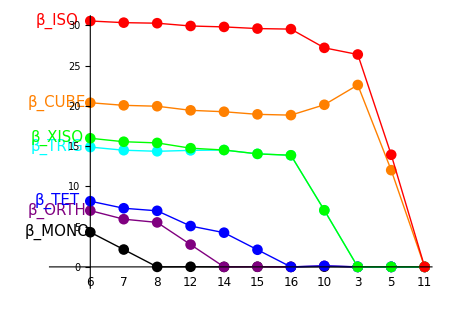

### Path through CUBE